```mathematica
RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

291

133

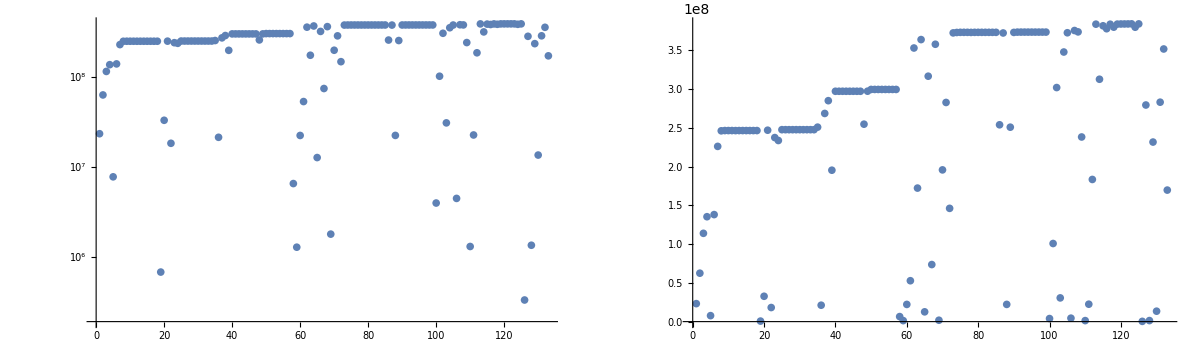

```mathematica
GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

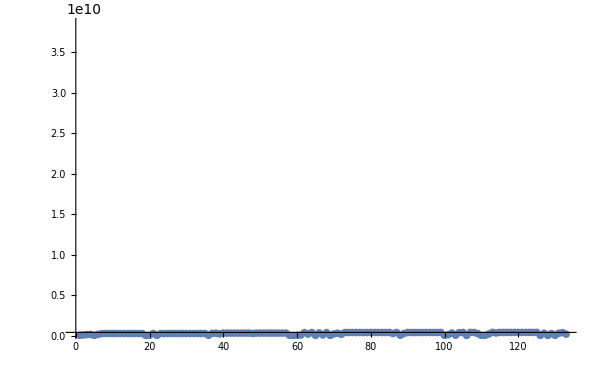

```mathematica
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{3.8401*^10,All},
Joined->False,
ImageSize->600
]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

QA10361kG : 0.5095952651
QA10371kG : 3.5214e-6
QE10425kG : 0.3438143144
QE10441kG : 0.0186626229
QE10511kG : 0.2846475137
QE10525kG : 0.0797149418
twissCalculationFraction : 0.7
PDrive_mean_x : 4.3071e-6
PDrive_mean_y : -4.3609e-6
PDrive_sigma_x : 0.0003965853
PDrive_sigma_y : 0.000652444
PDrive_mean_xp : 1.6784e-6
PDrive_mean_yp : 4.2265e-6
PDrive_twiss_beta_x : 7.5113809814
PDrive_twiss_alpha_x : 0.5327153777
PDrive_twiss_beta_y : 8.1538736281
PDrive_twiss_alpha_y : 2.9347189523
PDrive_median_x : -6.8285e-6
PDrive_median_y : -4.9121e-6
PDrive_median_xp : 7.69e-8
PDrive_median_yp : -5.921e-7
PDrive_emitSI_x : 1.9233e-6
PDrive_emitSI_y : 2.338e-6
PDrive_norm_emit_x : 5.4474e-6
PDrive_norm_emit_y : 8.6859e-6
PDrive_BMAG_x : 5.170413194
PDrive_BMAG_y : 3.1006184291
PDrive_BMAG_emit_x : 0.0000281652
PDrive_BMAG_emit_y : 0.0000269316
PDrive_BMAG_emitSI_x : 9.9441e-6
PDrive_BMAG_emitSI_y : 7.2493e-6
PDrive_zCentroid : 10.1161411831
PWitness_mean_x : 0.0000166492
PWitness_mean_y : -0.0000331775
PWitness_sigma_x : 0.0002825273
PWitness_sigma_y : 0.0010008309
PWitness_mean_xp : -5.5337e-6
PWitness_mean_yp : 0.0000125379
PWitness_twiss_beta_x : 5.4233408008
PWitness_twiss_alpha_x : 2.7988956923
PWitness_twiss_beta_y : 57.9599951354
PWitness_twiss_alpha_y : 21.1711545466
PWitness_median_x : 0.0000172275
PWitness_median_y : -5.982e-7
PWitness_median_xp : -0.0000150802
PWitness_median_yp : -2.4584e-6
PWitness_emitSI_x : 8.126e-7
PWitness_emitSI_y : 4.7339e-6
PWitness_norm_emit_x : 4.3233e-6
PWitness_norm_emit_y : 5.9798e-6
PWitness_BMAG_x : 13.0936161074
PWitness_BMAG_y : 21.2217769496
PWitness_BMAG_emit_x : 0.0000566076
PWitness_BMAG_emit_y : 0.0001269029
PWitness_BMAG_emitSI_x : 0.0000106394
PWitness_BMAG_emitSI_y : 0.0001004611
PWitness_zCentroid : 10.1160594039
bunchSpacing : -0.0000817791
transverseCentroidOffset : 0.0000313484
lostChargeFraction : 0.
errorTerm_lostChargeFraction : 0.
errorTerm_mainObjective : 5.2e-9
maximizeMe : 3.84110547493816972e8

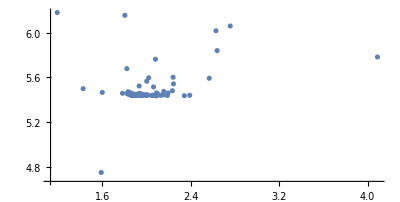

```mathematica
Show[
ListPlot[{
10^6#["PDrive_emitSI_x"],
10^6#["PDrive_norm_emit_x"]
}&/@raw,
AspectRatio->Automatic,PlotRange->All],
Plot[x,{x,0,50},PlotStyle->Red]
]
```

## Plot all

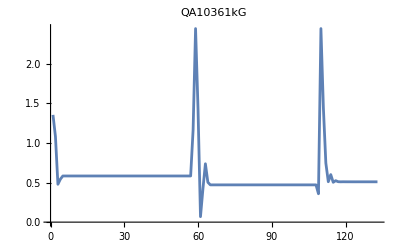
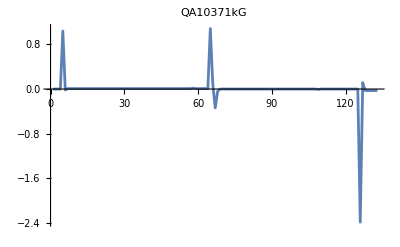
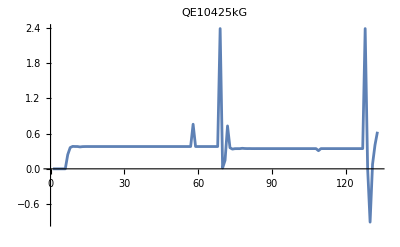
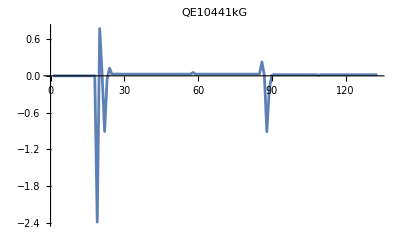
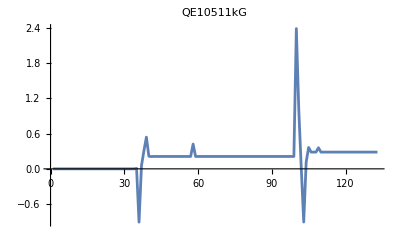
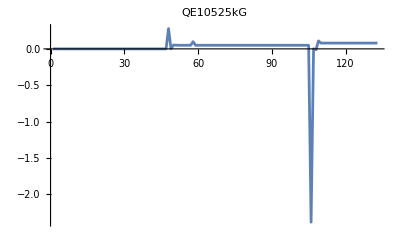
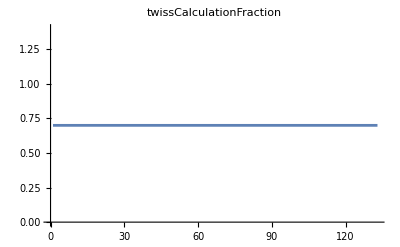
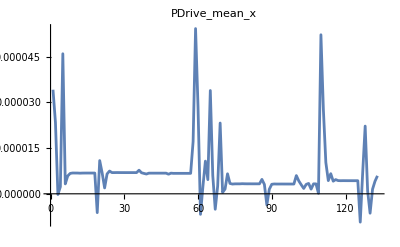
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{QA10361kG,QA10371kG,QE10425kG,QE10441kG,QE10511kG,QE10525kG}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

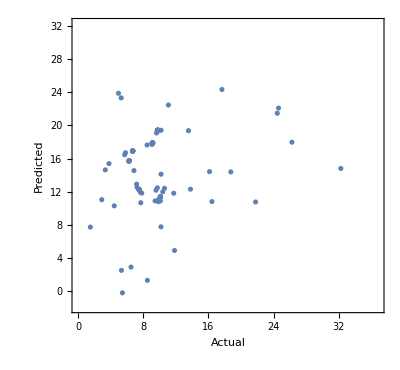

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
QA10361kG | 1 | 23601.1 | 23601.1 | 40.6155 | 3.18218×10^-9
QA10371kG | 1 | 56026.5 | 56026.5 | 96.4168 | 3.01897×10^-17
QE10425kG | 1 | 1.97901 | 1.97901 | 0.0034057 | 0.953556
QE10441kG | 1 | 25396.8 | 25396.8 | 43.7057 | 9.74206×10^-10
QE10511kG | 1 | 243.27 | 243.27 | 0.418647 | 0.51879
QE10525kG | 1 | 3365.29 | 3365.29 | 5.79137 | 0.0175565
Error | 126 | 73216.9 | 581.087 |  | 
Total | 132 | 181852. |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | Missing[KeyAbsent,L1PhaseSet] | 20.312+Missing[KeyAbsent,L1PhaseSet]
L2PhaseSet | -38.6737 | Missing[KeyAbsent,L2PhaseSet] | 38.6737+Missing[KeyAbsent,L2PhaseSet]
L3PhaseSet | -1.46329 | Missing[KeyAbsent,L3PhaseSet] | 1.46329+Missing[KeyAbsent,L3PhaseSet]
S1EL_xOffset | 0.000385255 | Missing[KeyAbsent,S1EL_xOffset] | -0.000385255+Missing[KeyAbsent,S1EL_xOffset]
S1EL_yOffset | -0.000241114 | Missing[KeyAbsent,S1EL_yOffset] | 0.000241114+Missing[KeyAbsent,S1EL_yOffset]
S2EL_xOffset | -0.00141787 | Missing[KeyAbsent,S2EL_xOffset] | 0.00141787+Missing[KeyAbsent,S2EL_xOffset]
S2EL_yOffset | 0.0000111705 | Missing[KeyAbsent,S2EL_yOffset] | -0.0000111705+Missing[KeyAbsent,S2EL_yOffset]
S2ER_xOffset | -0.00223816 | Missing[KeyAbsent,S2ER_xOffset] | 0.00223816+Missing[KeyAbsent,S2ER_xOffset]
S2ER_yOffset | -0.000675996 | Missing[KeyAbsent,S2ER_yOffset] | 0.000675996+Missing[KeyAbsent,S2ER_yOffset]
S1ER_xOffset | 0.00100714 | Missing[KeyAbsent,S1ER_xOffset] | -0.00100714+Missing[KeyAbsent,S1ER_xOffset]
S1ER_yOffset | 0.000398456 | Missing[KeyAbsent,S1ER_yOffset] | -0.000398456+Missing[KeyAbsent,S1ER_yOffset]
XC1FFkG | 0.206455 | Missing[KeyAbsent,XC1FFkG] | -0.206455+Missing[KeyAbsent,XC1FFkG]
XC3FFkG | -0.0899164 | Missing[KeyAbsent,XC3FFkG] | 0.0899164+Missing[KeyAbsent,XC3FFkG]
YC1FFkG | -0.0022312 | Missing[KeyAbsent,YC1FFkG] | 0.0022312+Missing[KeyAbsent,YC1FFkG]
YC2FFkG | -0.00851158 | Missing[KeyAbsent,YC2FFkG] | 0.00851158+Missing[KeyAbsent,YC2FFkG]